100

0.1

0.15

0.05

9.8

147. Cos[θ1[t]]+0.98 (0.15 Cos[θ1[t]]+0.05 Cos[θ2[t]])+1.125 θ1'[t]^2+0.05 (0.0225 θ1'[t]^2+0.015 Cos[θ1[t]-θ2[t]] θ1'[t] θ2'[t]+0.0025 θ2'[t]^2)

{147.147 Sin[θ1[t]]+0.00075 Sin[θ1[t]-θ2[t]] θ1'[t] θ2'[t]+2.25 θ1''[t]+0.05 (-0.015 Sin[θ1[t]-θ2[t]] (θ1'[t]-θ2'[t]) θ2'[t]+0.045 θ1''[t]+0.015 Cos[θ1[t]-θ2[t]] θ2''[t])==0,0.049 Sin[θ2[t]]-0.00075 Sin[θ1[t]-θ2[t]] θ1'[t] θ2'[t]+0.05 (-0.015 Sin[θ1[t]-θ2[t]] θ1'[t] (θ1'[t]-θ2'[t])+0.015 Cos[θ1[t]-θ2[t]] θ1''[t]+0.005 θ2''[t])==0}

{θ1[0]==π/2,θ1'[0]==0,θ2[0]==π,θ2'[0]==0.001}

{{θ1→InterpolatingFunction[…],θ2→InterpolatingFunction[…]}}

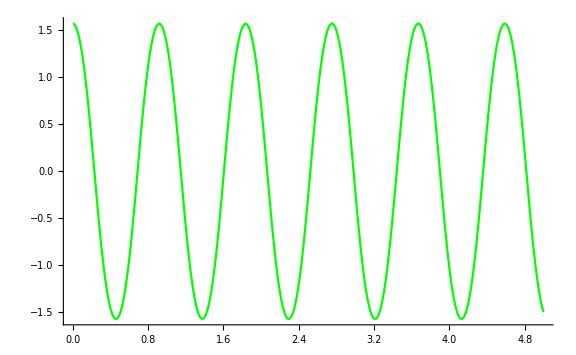

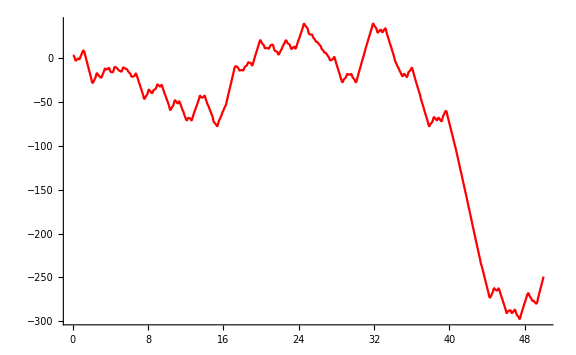

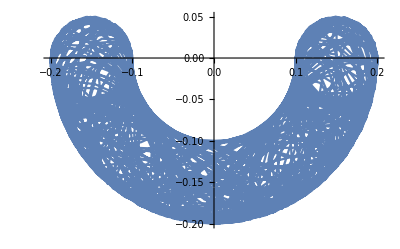

```mathematica
m1=100
m2=0.100
l1=0.15
l2=0.05
g=9.8
L=1/2*m1*l1^2*(θ1'[t])^2+1/2*m2*(l1^2*(θ1'[t])^2+l2^2*(θ2'[t])^2+2*l1*l2*θ1'[t]*θ2'[t]*Cos[θ1[t]-θ2[t]])+m1*g*l1*Cos[θ1[t]]+m2*g*(l1*Cos[θ1[t]]+l2*Cos[θ2[t]])

s={D[(D[L,θ1'[t]]), t]-D[L,θ1[t]]==0,
D[(D[L,θ2'[t]]), t]-D[L,θ2[t]]==0}
ics={θ1[0]==Pi/2,θ1'[0]==0,θ2[0]==Pi,θ2'[0]==0.001}
sol=NDSolve[{s,ics},{θ1,θ2},{t,0,50}]
(*[Evaluate[l1*Sin[θ1[t]]/.sol],{t,0,10},PlotRange->All,PlotStyle->Green,ImageSize->Large]
Plot[Evaluate[(l1*Sin[θ1[t]]+l2*Sin[θ2[t]])/.sol],{t,0,10},PlotRange->All,PlotStyle->Red,ImageSize->Large]*)
Plot[Evaluate[θ1[t]/.sol],{t,0,5},PlotRange->All,PlotStyle->Green,ImageSize->Large]
Plot[Evaluate[θ2[t]/.sol],{t,0,50},PlotRange->All,PlotStyle->Red,ImageSize->Large]
ParametricPlot[Evaluate[{(l1*Sin[θ1[t]]+l2*Sin[θ2[t]]),-(l1*Cos[θ1[t]]+l2*Cos[θ2[t]])}/.sol],{t,0,50},PlotRange->All,ImageSize->Full]
```